```mathematica
SqExp[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]^2/(2ℓ)]
OrnsteinUhlenbeck[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]/ℓ]
Matern[ν_][ℓ_][a_,b_]:=With[{r=EuclideanDistance[a,b]},
2^(1-ν)/Gamma[ν]((√(2ν)r)/ℓ)^ν BesselK[ν,(√(2ν)r)/ℓ]]

SqExpC[ℓ_]:=Compile[{{a,_Real},{b,_Real}},Exp[-Abs[a-b]^2/(2 ℓ^2)]]
OrnsteinUhlenbeckC[ℓ_]:=Compile[{{a,_Real},{b,_Real}},Exp[-Abs[a-b]/ℓ]]

Block[{ℓ,a,b},
Matern[3/2][ℓ_][a_,b_]:=Evaluate[Matern[3/2][ℓ][a,b]//FullSimplify];
Matern[5/2][ℓ_][a_,b_]:=Evaluate[Matern[5/2][ℓ][a,b]//FullSimplify];
Matern[7/2][ℓ_][a_,b_]:=Evaluate[Matern[7/2][ℓ][a,b]//FullSimplify]]
```

```mathematica
Krig[Kernel_,X_,Y_]:=Krig[Kernel,X,Y,0]

Krig[Kernel_,X_,Y_,v_]:=
With[{Σ22=Outer[Kernel,X,X]+v IdentityMatrix[Length[X]]},
With[{Σ22i=LinearSolve[Σ22]},
Compile[{{p,_Real}},
Module[{μ,σ2,Σ,Σ11,Σ12,Σ21},
Σ11=Outer[Kernel,{p},{p}];
Σ12=Outer[Kernel,{p},X];
Σ21=Transpose[Σ12];
μ=Dot[Σ12,Σ22i[Y]]//First;
Σ=Σ11-Dot[Σ12,Σ22i[Σ21]];
σ2=Σ⟦1,1⟧;
{μ,σ2}],
RuntimeOptions->{
"EvaluateSymbolically"->False},
CompilationOptions->{
"ExpressionOptimization"->True,
"InlineExternalDefinitions"->True,
"InlineCompiledFunctions"->True}]]]
```

```mathematica
KrigPlot[Kernel_,X_,Y_]:=KrigPlot[Kernel,X,Y,0]

KrigPlot[Kernel_,X_,Y_,v_]:=
With[{f=Krig[Kernel,X,Y,v]},
Block[{μ,σ,σ2,plotf},
plotf[body_]:=With[{module=Module},
Function[{x},module[{μ,σ,σ2},{μ,σ2}=f[x];σ=√σ2;body]]];

With[{
mean=plotf[μ],
low=plotf[μ-σ],
high=plotf[μ+σ]
},
Plot[{mean[x],low[x],high[x]},{x,0,1},
PlotRange->{-1.1,1.5},
PlotStyle->{Dashed,None,None},
Filling->{2->{3}}]
]]]
```

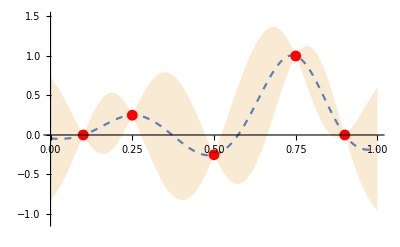

```mathematica
With[{
Y={0,1/4,-1/4,1,0},
X={1/10,1/4,1/2,3/4,9/10}},
Show[
KrigPlot[SqExpC[0.1],X,Y],
ListPlot[Transpose[{X,Y}],
PlotStyle->Red]]]
```

```mathematica
Manipulate[
Module[{X,Y},
{X,Y}=Transpose[p];
KrigPlot[Kernel[ℓ],X,Y]],
{{p,{{1/2,3/4},{3/4,-3/4},{1/4,-1/10}}},
{0,-1},{1,1},Locator},
{Kernel,{SqExpC,OrnsteinUhlenbeckC,Matern[3/2],Matern[5/2]}},
{{ℓ,0.1},0.01,0.2},
SaveDefinitions->True]
```

```mathematica
ExpectedGainC=
Compile[{{μ,_Real},{σ,_Real},{ts,_Real}},
Module[{t},
t=(ts-μ)/σ;
σ((ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)])],
CompilationOptions->{"ExpressionOptimization" -> False},
RuntimeOptions->{"EvaluateSymbolically"->False}]
```

CompiledFunction[…]

```mathematica
ExpectedGainPlot[Kernel_,X_,Y_,t_]:=
With[{f=Krig[Kernel,X,Y]},
Block[{μ,σ,σ2,plotf},
plotf[body_]:=With[{module=Module},
Function[{x},module[{μ,σ,σ2},{μ,σ2}=f[x];σ=√σ2;body]]];

With[{
mean=plotf[μ],
low=plotf[μ-σ],
high=plotf[μ+σ],
exgain=plotf[ExpectedGainC[μ,σ,t]]
},
Plot[{mean[x],low[x],high[x],t,exgain[x]},{x,0,1},
PlotRange->{-1.1,1.5},
PlotStyle->{Dashed,None,None,Automatic,Automatic},
Filling->{2->{3}}]
]]]
```

```mathematica
Manipulate[
Module[{X,Y,t},
{X,Y}=Transpose[p];
t=Max[Y];
ExpectedGainPlot[Kernel[ℓ],X,Y,t]],
{{p,{{1/2,0},{1/4,1/4},{9/10,1/10}}},
{0,-1},{1,1.5},Locator},
{Kernel,{SqExpC,OrnsteinUhlenbeckC,Matern[3/2],Matern[5/2]}},
{{ℓ,0.2},0.01,0.4},
SaveDefinitions->True]
```

```mathematica
Periodic[ν_][ℓ_][a_,b_]:=
With[{r=EuclideanDistance[a,b]},
Exp[-(2 Sin[ν r/2]^2)/ℓ^2]]

DampedPeriodic[ν_][ℓ_][d_][a_,b_]:=
With[{r=EuclideanDistance[a,b]},
Exp[-r/d]Exp[-(2 Sin[ν r/2]^2)/ℓ^2]]
```

```mathematica
Manipulate[
Plot[
DampedPeriodic[ν][ℓ][d][0,x],
{x,0,1},
PlotRange->{0,1}],
{{ν,20.0},1.0,50.0},
{{ℓ,0.5},0.01,0.8},
{{d,0.5},0.01,0.8}]
```

```mathematica
Manipulate[
Module[{X,Y,t},
{X,Y}=Transpose[p];
KrigPlot[DampedPeriodic[ν][ℓ][d],X,Y]],
{{p,{{1/10,0},{2/10,1/4},{3/10,-1/4}}},
{0,-1},{1,1.5},Locator},
{{ν,20.0},0.5,30.0},
{{ℓ,1.6},0.4,2.0},
{{d,4.0},0.4,8.0},
SaveDefinitions->True]
```

```mathematica
Manipulate[
Module[{X,Y,t},
{X,Y}=Transpose[p];
t=Max[Y];
KrigNoisePlot[Kernel[ℓ],X,Y,v]],
{{p,{{1/2,0},{1/4,1/4},{9/10,1/10}}},
{0,-1},{1,1.5},Locator},
{Kernel,{SqExpC,OrnsteinUhlenbeckC,Matern[3/2],Matern[5/2]}},
{{ℓ,0.2},0.01,0.4},
{{v,0.5},0,2},
SaveDefinitions->True]
```